```mathematica
Clear[α,βi,β1,β2,β3,β4,β5,βA,βB,gH,h,κ,θ,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,hz,Gauss,γ,F0a,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB,λ,δ,M2];
ΔA=(√(-α-gH h^2 Cos[π/2]^2 Sin[π/2]^2))/(√2 √(β2+β4+β5));
ΔB=(√(-gH h^2-3 α))/(√2 √(3 β1+3 β2+β3+β4+β5));
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
(********************************)
βi=2 β1+8 β2+3 β3+5 β4+3 β5;
M2=2/ϕ0^2 (-2 α ΔA^2+(α+1/3 gH h^2) ΔB^2+2/3 √6 α ΔA ΔB+1/3 ΔA^2 ΔB^2 βi );
δ=-3/ϕ0^3 (2 α ΔA^2-(√6)/3 (4 α+1/3 gH h^2) ΔA ΔB+2/3 ΔA^2 ΔB^2 βi);
λ=4/ϕ0^4 (-1/2 α ΔA^2+(√6)/9 ΔA ΔB (6 α+gH h^2)-(1/6) (3 α+gH h^2) ΔB^2+1/3 ΔA^2 ΔB^2 βi);
fx=FullSimplify[λ/δ^2 M2,Assumptions->{{ϕ,ϕ0,Δ,ΔA,ΔB,h,θ,κ,gH,α,β1,β2,β3,β4,β5}∈Reals,α<0,ϕ>0,ϕ0>0,ΔA>0,ΔB>0,h>0,gH>0,κ>0}];
(***********************************************)
```

1.14039×10^51

-0.7775

*******************

-3.42041×10^-31

4.13941×10^40

*******************

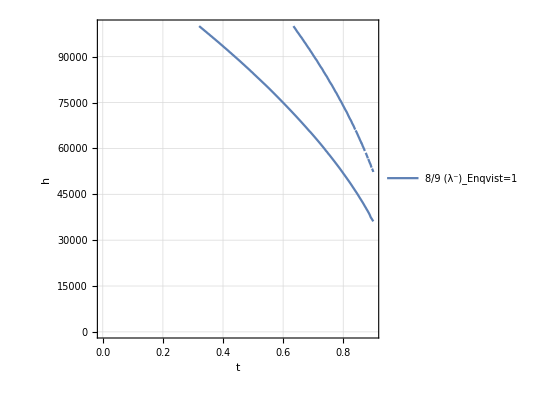

```mathematica
m=1;s=1;J=1;kg=1;k=1;Gauss=1;hz=1/s;
c=2.99792458 10^8 m s^-1;
hbar=1.054571817 10^-34 J s ;(* plank constant *)
kb=1.380649 10^-23 J k^-1;(**J.K^-1*)
(*π=3.1415926;*)
u= 1.66053906660 10^-27 kg ;
m3=3.016293 u;
(**pressure is 32 bar**)
ms=5.66 m3;
Tc=2.463 10^-3 k^-1;(*mK, kevin*)
vf=32.85 m s^-1;
kf=(vf ms)/hbar;
Nf=(ms kf)/(2 π^2 hbar^2)
γ=-3243.409942 hz Gauss^-1;
F0a=−0.7775

c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
(**pressure is 4 bar**)
(*ms=3.27 m3;
Tc=1.388 10^-3 k^-1;(*mK, kevin*)
vf=52.36 m s^-1;
kf=(vf ms)/hbar;
Nf=(ms kf)/(2 π^2 hbar^2)
γ=-3243.409942 hz Gauss^-1;
F0a=−0.7392

c1=-0.0155;c2 = -0.0562;c3=-0.0184;c4=-0.0514;c5=-0.1602;*)
(*******  All βi ********)
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
Print[Style["*******************",Red,18]]
γ hbar
gH=5 Abs[βwc1] ((γ hbar)/(1+F0a))^2
(*gH=5 Abs[βwc1]/(1+F0a)^2 (-2.1 10^-30)^2*)
Print[Style["*******************",Red,18]]
α=1/3 Nf (t-1);
(******************************************)
ContourPlot[λ/δ^2 M2==1/4,{t,0,0.9},{h,0,100000},GridLines->Automatic,PlotLegends->{"8/9 (λ^-)_Enqvist=1"},FrameLabel->{"t","h"}]
```